```mathematica
Lab 4
Variant 5
```

```mathematica
EulerForFirstTask[u0_, p_, q_, n_, h_, X_]:= Block[{Z1, k},
Z1={ u0};
For[k=1, k<n, k++,
AppendTo[Z1,0]; 
];
For[k=1, k<n, k++,
Z1⟦k+1⟧=Z1⟦k⟧+h*(-Z1⟦k⟧*Z1⟦k⟧ - p[X⟦k⟧]*Z1⟦k⟧ + q[X⟦k⟧])//N; 
];
Return[Z1];
];

EulerForSecondTask[u0_, p_, q_, n_, h_, X_,Z1_, f_]:= Block[{ Z2, k},
Z2={ u0};
For[k=1, k<n, k++,
AppendTo[Z2,0]; 
];
For[k=1, k<n, k++,
Z2⟦k+1⟧=Z2⟦k⟧+h*(-Z2⟦k⟧*(Z1⟦k⟧ + p[X⟦k⟧] ) + f[X⟦k⟧])//N; 
];
Return[Z2];
];

EulerForThirdTask[u0_, n_, h_,X_,  Z1_, Z2_]:= Block[{ Y, k},
Y={};
For[k=0, k<n, k++,
AppendTo[Y,0]; 
];
Y⟦n⟧=u0;
For[k=n-1, k> 0, k--,
Y⟦k⟧=Z2⟦k+1⟧-h*(Z1⟦k+1⟧*Y⟦k+1⟧ + Z2⟦k+1⟧)//N; 
];
Return[Y];
];

(*=================================================================== *)

EulerForFourthTask[u0_,p_,q_,n_, h_, X_]:= Block[{ U1, k},
U1={ u0};
For[k=1, k<n, k++,
AppendTo[U1,0]; 
];
Print["U1: ", U1];
For[k=1, k<n, k++,
U1⟦k+1⟧=U1⟦k⟧+h*(-U1⟦k⟧*U1⟦k⟧*q[X⟦k⟧] + U1⟦k⟧ *p[X⟦k⟧]+ 1)//N; 
];
Return[U1];
];

EulerForFifthTask[u0_,p_,q_, n_, h_,X_,U1_, f_]:= Block[{ U2, k},
U2={ u0};
For[k=1, k<n, k++,
AppendTo[U2,0]; 
];
Print["U2: ", U2];
For[k=1, k<n, k++,
U2⟦k+1⟧=U2⟦k⟧+h*(-U1⟦k⟧*( U2⟦k⟧*q[X⟦k⟧] + f[X⟦k⟧]))//N; 
];
Return[U2];
];

EulerForSixTask[u0_,n_, h_, X_,  U1_, U2_]:= Block[{ Y, k},
Y={};
For[k=0, k<n-1, k++,
AppendTo[Y,0]; 
];
AppendTo[Y,u0];
Print["Y: ", Y];
For[k=n-1, k>0, k--,
Y⟦k⟧=Y⟦k+1⟧-h*(Y⟦k+1⟧- U2⟦k+1⟧)/U1⟦k+1⟧; //N; 
];
Return[Y];
];
```

```mathematica
(* Начальные условия *)
p[x_]:= 2*x;
q[x_]:= 1;
f[x_]:= 2*(x^2+1)*Cos[x];
a=0;
b=0.5;
n=20;
h=(b-a)/n;

(* Формируем сетку Х *)
X={};
For[k=0, k<n, k++,
AppendTo[X,a+k*h //N]
];

(* Начальные условия *)
α0 = 1;
β0 = 0;
γ0 = 0;
α1 = 1;
β1 = 0;
γ1 = 1/2*Sin[1/2]; //N

Y={};

If[β0 ≠ 0, 
u0=-α0/β0; (* Начальное значение для Z1 *)
Z1 = EulerForFirstTask[u0, p,q, n, h, X];
u1 = γ0/β0;
Z2 = EulerForSecondTask[u1,p,q,  n, h,X, Z1,  f];
 u2= (γ1-β1*Z2⟦n⟧)/(α1+β1*Z1⟦n⟧);
Y = EulerForThirdTask[u2, n, h , X, Z1, Z2];
 ];

If[α0 ≠ 0, 
u0=-β0/α0;
Print["u0: ", u0];
U1 = EulerForFourthTask[u0,p,q,n, h, X]; 
Print["U1: ", U1];
u1 = γ0/α0;
Print["u1: ", u1];
U2 = EulerForFifthTask[u1,p,q, n, h,X,U1, f];
Print["U2: ", U2];
u2= (γ1*U1⟦n⟧+β1*U2⟦n⟧)/(β1+α1*U1⟦n⟧);
Print["u2: ", u2];
Y = EulerForSixTask[u2,n, h, X,  U1, U2];
Print["Y: ",Y];
 ];
```

u0: 0

U1: {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

U1: {0,0.025,0.0500156,0.0750781,0.100219,0.125469,0.150859,0.176422,0.202187,0.228187,0.254453,0.281015,0.307904,0.335153,0.362791,0.390849,0.419359,0.448349,0.477851,0.507894}

u1: 0

U2: {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

U2: {0,0.,-0.00125039,-0.00375273,-0.00751009,-0.012527,-0.0188095,-0.0263646,-0.0352007,-0.045327,-0.0567532,-0.0694898,-0.083547,-0.0989352,-0.115664,-0.133742,-0.153177,-0.173974,-0.196136,-0.219663}

u2: 0.239713

Y: {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.239713}

Y: {-2.1684×10^-19,0.00184936,0.00494717,0.00929033,0.0148742,0.0216925,0.0297376,0.0390002,0.0494695,0.0611331,0.0739774,0.0879871,0.103145,0.119434,0.136834,0.155323,0.174881,0.195481,0.217101,0.239713}

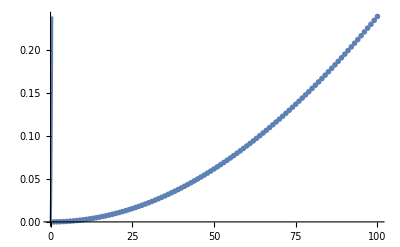

```mathematica
u[x_]:= x*Sin[x];
G1 = Plot[u[x], {x,a, b}];
G2 = ListPlot[Y,PlotStyle-> PointSize[0.01]]; 
Show[G2,G1]
(* Неправильно *)
```